## Fuel Cell

```mathematica
ucell:=Enernst-uact-uohmic-ucon
```

Nernst equation

```mathematica
Enernst:=dG/(2 F)+dS/(2 F)(T-Tref)+(R T)/(2 F)Log[(Ph2 √Po2)/P0]
```

```mathematica
uact=-(ksi1+ksi2 T + ksi3 T Log[Co2]+ksi4 T Log[iFC]);
```

```mathematica
uohmic=(rhoM l)/A
```

0.004 rhoM

```mathematica
rhoM=(181.6 (1+0.03(iFC/(A 10^4))+0.062(T/303)^2(iFC/(A 10^4))^2.5))/(psi-0.634-3(iFC/(A 10^4))E^(4.18((T-303)/T)))
```

(181.6 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

```mathematica
uohmic
```

(0.7264 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

```mathematica
Co2=Po2/(5.08 10^6 E^(-498/T))
```

1.92714×10^-7

```mathematica
ucon=-B Log[1-J/Jmax]
```

-0.15 Log[1-0.0238095 iFC]

## Conductances

```mathematica
conA=iFC/(uact+ucon)
```

iFC/(0.117673-0.15 Log[1-0.0238095 iFC]+0.0342865 Log[iFC])

```mathematica
conOhm=iFC/(uohmic)
```

(1.37665 (22.366-0.0621794 iFC) iFC)/(1+0.00048 iFC+2.28145×10^-6 iFC^2.5)

```mathematica
Enernst
```

1.19719

```mathematica
ksi2:=0.00286+0.0002 Log[A 10^4]+4.3 10^-5 Log[Ch2]
```

```mathematica
dS=.85 10^-3 2F
```

164.025

```mathematica
psi=23.;T=300;
```

```mathematica
F=96485.33212;
R=8.314;
Tref=298.15;
dG=228000.6;
P0=1;
```

```mathematica
n=48;
T=323;
A=62.5 10^-4;
l=25 10^-6;
Ph2=1.476;
Po2=0.2095;
B=0.15;
Rc=0.0003;ksi1=-.948;ksi3=7.22 10^-5;ksi4=-1.0615 10^-4;
psi=23;
Jmax=672 10^-3 10^4;
Jn=22 10^-3 10^4;
Imax=42;
```

```mathematica
J=iFC/A
```

160. iFC

```mathematica
ksi2:=0.00286+0.0002 Log[A 10^4]+4.3 10^-5 Log[Ch2]
```

```mathematica
Ch2=1;
```

```mathematica
ucell
```

1.07952-(0.7264 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)+0.15 Log[1-0.0238095 iFC]-0.0342865 Log[iFC]

```mathematica
Enernst
```

1.19719

```mathematica
conA=iFC/(uact+ucon)
```

iFC/(0.117673-0.15 Log[1-0.0238095 iFC]+0.0342865 Log[iFC])

```mathematica
rhoM
```

(181.6 (1+0.00048 iFC+2.28145×10^-6 iFC^2.5))/(22.366-0.0621794 iFC)

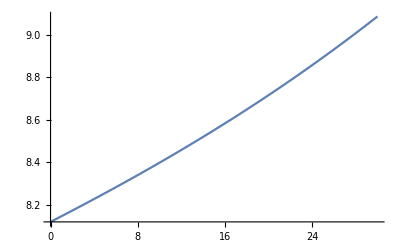

```mathematica
Plot[rhoM,{iFC,0,30}]
```

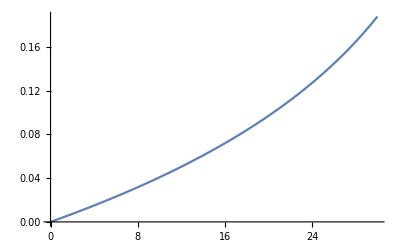

```mathematica
Plot[ucon,{iFC,0,30}]
```

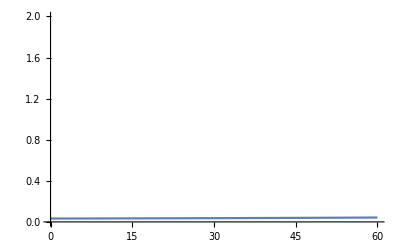

```mathematica
Plot[uohmic,{iFC,0,60},PlotRange->{0,2}]
```

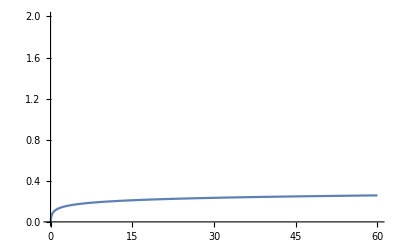

```mathematica
Plot[uact,{iFC,0,60},PlotRange->{0,2}]
```

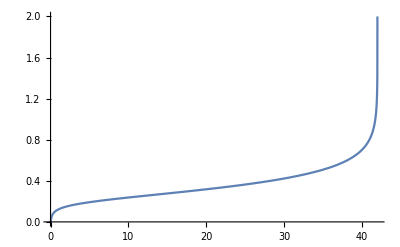

```mathematica
Plot[{uact+ucon},{iFC,0,60},PlotRange->{0,2}]
```

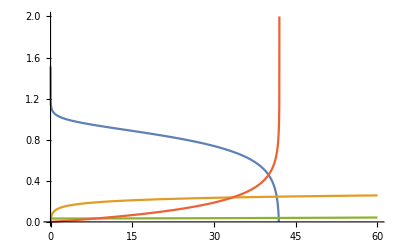

```mathematica
Plot[{ucell,uact,uohmic,ucon},{iFC,0,60}, PlotRange->{0,2}]
```

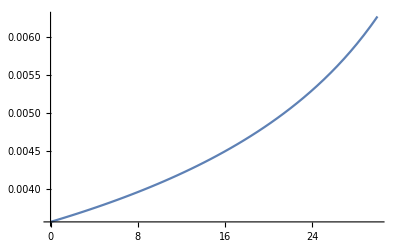

```mathematica
Plot[ucon/iFC,{iFC,0,30}]
```

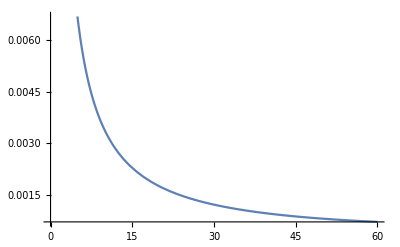

```mathematica
Plot[uohmic/iFC,{iFC,0,60}]
```

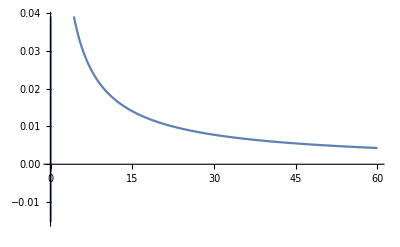

```mathematica
Plot[uact/iFC,{iFC,0,60}]
```

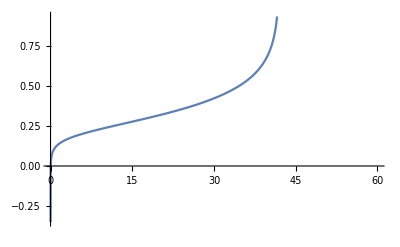

```mathematica
Plot[{uact+ucon},{iFC,0,60}]
```

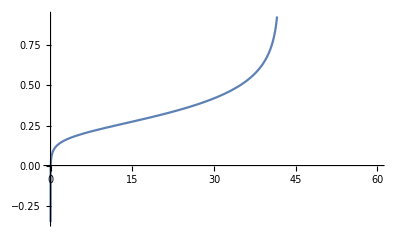

-Graphics-

```mathematica
Nernst
```

Nernst

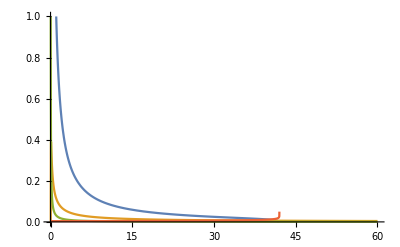

```mathematica
Plot[{ucell/iFC,uact/iFC,uohmic/iFC,ucon/iFC},{iFC,0,60}, PlotRange->{0,01}]
```

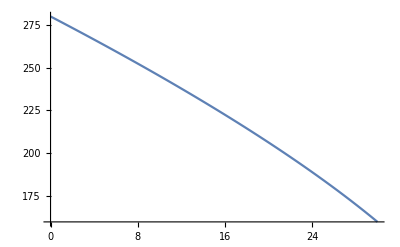

```mathematica
Plot[iFC/ucon,{iFC,0,30}]
```

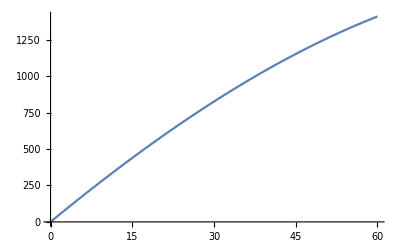

```mathematica
Plot[iFC/uohmic,{iFC,0,60}]
```

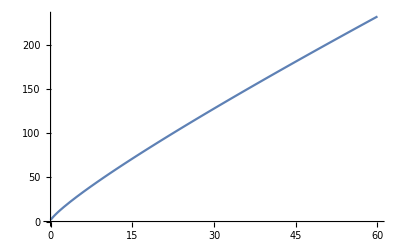

```mathematica
Plot[iFC/uact,{iFC,0,60}]
```

```mathematica
conA=iFC/(uact+ucon)
```

iFC/(0.117673-0.15 Log[1-0.0238095 iFC]+0.0342865 Log[iFC])

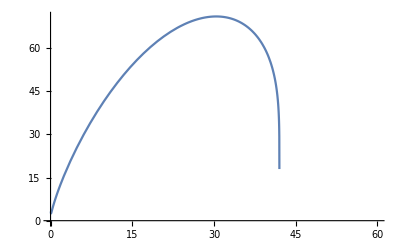

```mathematica
Plot[iFC/(uact+ucon),{iFC,0,60}]
```

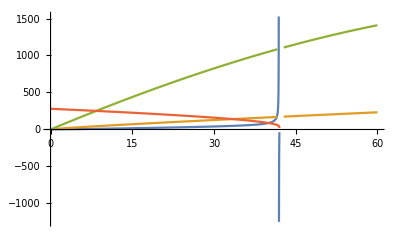

```mathematica
Plot[{iFC/ucell,iFC/uact,iFC/uohmic,iFC/ucon},{iFC,0,60}]
```

```mathematica
422./834
```

0.505995

```mathematica
2*200./8140
```

0.04914